### Two Trader Equilibrium in the OW Model - Exact Solution

#### Define cost functions

```mathematica
(*Input variables*)
a0=0.0; (*Example value*)
a1=0.0; (*Example value*)
b0=0.0; (*Example value*)
b1=0.0; (*Example value*)
rho=10; (*Example value*)
lambda=2; (*Example value*)

(*Cost functions for traders A and B*)
Ca[a0_,a1_,b0_,b1_]:=Module[{mua,mub,c0,c1,mu,Disp,IDisp},
(*Calculations*)mua=1-a0-a1;
mub=1-b0-b1;
c0=a0+lambda*b0;
c1=a1+lambda*b1;
mu=mua+lambda*mub;
(*Define Disp[t]*)Disp[t_]:=c0 Exp[-rho t]+mu (1-Exp[-rho t])/rho;
IDisp=Integrate[Disp[t],{t,0,1}];
(*Calculating Ca*)1/2*(c0*a0+c1*a1)+mua*IDisp+Disp[1]*a1
];

Cb[a0_,a1_,b0_,b1_]:=Module[{mua,mub,c0,c1,mu,Disp,IDisp},
(*Calculations*)mua=1-a0-a1;
mub=1-b0-b1;
c0=a0+lambda*b0;
c1=a1+lambda*b1;
mu=mua+lambda*mub;
(*Define Disp[t]*)Disp[t_]:=c0 Exp[-rho t]+mu (1-Exp[-rho t])/rho;
IDisp=Integrate[Disp[t],{t,0,1}];
(*Calculating Cb*)lambda*(1/2*(c0*b0+c1*b1)+mub*IDisp+Disp[1]*b1)
];

(*Evaluate the Cost Functions*)
CaVal=Ca[a0,a1,b0,b1];
CbVal=Cb[a0,a1,b0,b1];

(*Display results*)
{CaVal,CbVal}
```

{0.270001,0.540003}

#### Calculate the Nash Equilibrium

FOC at the initial guess:

dCa/da0: -1.6016×10^-9

dCa/da1: -5.61547×10^-9

dCb/db0: 0.300661

dCb/db1: -0.172687

Equilibrium Solutions: {{a0→0.159361,a1→-0.00359776,b0→0.0896755,b1→0.0882016}}

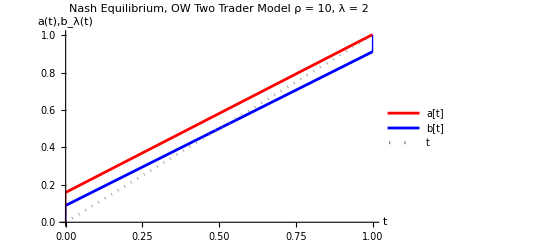

```mathematica
(*Clear any previous definitions*)Clear[a0,a1,b0,b1,rho,lambda]

(*Constants*)
rho=10;
lambda=2;

(*Redefine functions*)
Ca[a0_,a1_,b0_,b1_]:=Module[{mua,mub,c0,c1,mu,Disp,IDisp},
mua=1-a0-a1;
mub=1-b0-b1;
c0=a0+lambda*b0;
c1=a1+lambda*b1;
mu=mua+lambda*mub;
Disp[t_]:=c0 Exp[-rho t]+mu (1-Exp[-rho t])/rho;
IDisp=Integrate[Disp[t],{t,0,1}];
1/2*(c0*a0+c1*a1)+mua*IDisp+Disp[1]*a1];

Cb[a0_,a1_,b0_,b1_]:=Module[{mua,mub,c0,c1,mu,Disp,IDisp},
mua=1-a0-a1;
mub=1-b0-b1;
c0=a0+lambda*b0;
c1=a1+lambda*b1;
mu=mua+lambda*mub;
Disp[t_]:=c0 Exp[-rho t]+mu (1-Exp[-rho t])/rho;
IDisp=Integrate[Disp[t],{t,0,1}];
lambda*(1/2*(c0*b0+c1*b1)+mub*IDisp+Disp[1]*b1)];

(*Input values*)
initialValues={a0->0,a1->0,b0->0,b1->0};

(*Calculate partial derivatives symbolically*)
dCaDa0=D[Ca[a0,a1,b0,b1],a0];
dCaDa1=D[Ca[a0,a1,b0,b1],a1];
dCbDb0=D[Cb[a0,a1,b0,b1],b0];
dCbDb1=D[Cb[a0,a1,b0,b1],b1];

(*Evaluate partial derivatives at the initial values*)
evalDCaDa0=dCaDa0/. initialValues;
evalDCaDa1=dCaDa1/. initialValues;
evalDCbDb0=dCbDb0/. initialValues;
evalDCbDb1=dCbDb1/. initialValues;

(*Print partial derivatives*)
Print["FOC at the initial guess:"]
Print["dCa/da0: ",evalDCaDa0];
Print["dCa/da1: ",evalDCaDa1];
Print["dCb/db0: ",evalDCbDb0];
Print["dCb/db1: ",evalDCbDb1];

(*Solve for the variables that set all partial derivatives to zero*)
sol=Solve[{dCaDa0==0,dCaDa1==0,dCbDb0==0,dCbDb1==0},{a0,a1,b0,b1}];

(*Display solutions*)
Print["\nEquilibrium Solutions: ",N[sol]];

(*Check if the solution exists before using it*)If[Length[sol]>0,(*Extract solutions*){a0sol,a1sol,b0sol,b1sol}={a0,a1,b0,b1}/. sol[[1]],Print["No solutions found."]];

(*New definitions based on provided formula*)aFunc[t_]:=Piecewise[{{0,t==0},{a0sol+(1-a0sol-a1sol)*t,0<t<1},{1,t==1}}];
bFunc[t_]:=Piecewise[{{0,t==0},{b0sol+(1-b0sol-b1sol)*t,0<t<1},{1,t==1}}];

(*Plot the functions with vertical lines*)
eps=0.001;
Plot[{aFunc[t],bFunc[t], t},{t,0,1},PlotStyle->{Red,Blue, {Gray, Dotted}},Epilog->{Red,Line[{{0,0},{0,aFunc[eps]}}],Line[{{1,aFunc[1-eps]},{1,1}}],Blue,Line[{{0,0},{0,bFunc[eps]}}],Line[{{1,bFunc[1-eps]},{1,1}}]},
PlotLegends->{"a[t]","b[t]", "t"},
PlotLabel->Row[{"Nash Equilibrium, OW Two Trader Model\n","ρ = ",rho,", λ = ",lambda}],
AxesLabel->{"t","a(t),b_λ(t)"},Ticks->Automatic]
```